# pi0 --> NN

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (development version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
dm[mu_]:=GA[mu]
dm[5]:=DiracMatrix[5]
ds[p_]:=DiracSlash[p]
mt[mu_,nu_]:=MetricTensor[mu,nu]
fv[p_,mu_]:=FourVector[p,mu]
epsilon[a_,b_,c_,d_]:=LeviCivita[a,b,c,d]
id[n_]:=IdentityMatrix[n]
sp[p_,q_]:=ScalarProduct[p,q]
li[mu_]:=LorentzIndex[mu]
prop[p_,m_]:=ds[p]+m
PR=dm[6];
PL=dm[7];
dσ[μ_,ν_]:=I/2(dm[μ].dm[ν]-dm[ν].dm[μ]);
SetOptions[{DiracMatrix, DiracSlash,LeviCivita, FourVector, MetricTensor, SetMandelstam, OneLoop, ScalarProduct},Dimension->4];
SetDirectory[NotebookDirectory[]]
```

/Users/matheushostert/Repos/nuSMEFT/mathematica

## pi0 ->ν(k1) v(k2)

```mathematica
PS2=1/(8π)√Lambda[1,(m1/mP)^2,(m2/mP)^2];FluxFactor=1/(2mP);SpinAverage=1/1;IdenticalFactor=1/2;
```

### Kinematics

```mathematica
subP={Pair[Momentum[k1],Momentum[k1]]-> m1^2,
Pair[Momentum[k2],Momentum[k2]]-> m2^2,
Pair[Momentum[k1],Momentum[k2]]-> (mP^2-m1^2-m2^2)/2}
Lambda[a_,b_,c_]:=(a-b-c)^2-4 b c
```

{OverBar[k1]^2→m1^2,OverBar[k2]^2→m2^2,OverBar[k1]·OverBar[k2]→1/2 (-m1^2-m2^2+mP^2)}

### Dirac Amplitudes

```mathematica
MAmp= Subscript[C, HN] vEW^2/Λ^2 * g/(2 cW)g/(2 cW)((Fpi( FourVector[k1,ν]+FourVector[k2,ν])SpinorU[k2,m2].((dm[μ].dm[5])/2+ (dm[μ].dm[5])/2).SpinorV[k1,m1])/(MZ^2))*mt[μ,ν]//DiracSimplify;
MAmpC=ComplexConjugate[MAmp]/.{μ->μ2 };Msqr=FermionSpinSum[MAmpC MAmp]/.{DiracTrace-> Tr}/.{K-> k1+k2}//Contract//ScalarProductExpand;
DecayRate=Msqr*SpinAverage*PS2*FluxFactor*IdenticalFactor/.subP//Simplify
```

-(Fpi^2 g^4 vEW^4 C_HN^2 (m1+m2)^2 (m1^2-2 m1 m2+m2^2-mP^2) √((-2 m1^2 (m2^2+mP^2)+m1^4+(m2^2-mP^2)^2)/mP^4))/(256 π cW^4 Λ^4 mP MZ^4)

```mathematica
Final = DecayRate/.{m1-> r1*mP,m2-> r2 mP,g-> √(8*cW^2*MZ^2 GF/(√2))}/.{r1-> -dR+r2}/.{r2-> (Rtot+dR)/2}//FullSimplify
```

-((dR^2-1) Fpi^2 GF^2 mP^3 Rtot^2 vEW^4 C_HN^2 √((dR^2-1) (Rtot^2-1)))/(8 π Λ^4)

```mathematica
FinalGF = Final/.{dR-> 0}//Simplify//PowerExpand//Simplify
```

(Fpi^2 GF^2 mP^3 Rtot^2 √(1-Rtot^2) vEW^4 C_HN^2)/(8 π Λ^4)

```mathematica
FinalGF*1.52*10^24*8.52*10^-17/.{GF-> 1.16*10^(-5),vEW-> 1,Λ-> 1,Rtot-> (2*0.001)/mP}/.{mP-> 0.140,Fpi-> 0.092}
```

3.28608×10^-12 C_HN^2

```mathematica
(Fpi^2 GF^2 mP^3 Rtot^2  vEW^4 Subscript[C, HN]^2)/(8 π Λ^4)*1.52*10^24*8.52*10^-17/.{GF-> 1.16*10^(-5),vEW-> 246,Rtot-> (2*mN)/mP}/.{mN-> 0.05,mP-> 0.135,Fpi-> 0.1307}/.{Λ-> 340}
```

4.38197×10^-9 C_HN^2

```mathematica
2.9509136393256387*^-8 GxoverGf^2 r^2/.{r-> 0.25}
```

1.84432×10^-9 GxoverGf^2

```mathematica
BRforpi0[r_]:=Evaluate[FinalGF*1.52*10^24*8.52*10^-17 /.{GF-> 1.16*10^(-5),dR-> 0,Rtot-> 2r,mP-> 0.135,Fpi-> 0.1307,Subscript[C, HN]-> 1,vEW-> 246.0,Λ-> 200}]
```

```mathematica
|
```

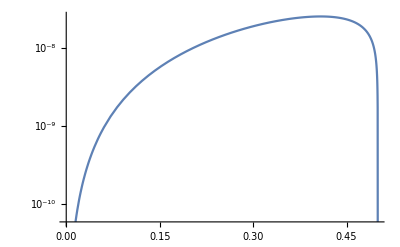

```mathematica
LogPlot[BRforpi0[x],{x,0,0.5}]
```

## eta ->ν(k1) v(k2)

```mathematica
PS2=1/(8π)√Lambda[1,(m1/Mz)^2,(m2/Mz)^2];FluxFactor=1/(2Mz);SpinAverage=1/1;
```

### Kinematics

```mathematica
subP={Pair[Momentum[k1],Momentum[k1]]-> m1^2,
Pair[Momentum[k2],Momentum[k2]]-> m2^2,
Pair[Momentum[k1],Momentum[k2]]-> (Mz^2-m1^2-m2^2)/2}
Lambda[a_,b_,c_]:=(a-b-c)^2-4 b c
```

{OverBar[k1]^2→m1^2,OverBar[k2]^2→m2^2,OverBar[k1]·OverBar[k2]→1/2 (-m1^2-m2^2+Mz^2)}

### Dirac Amplitudes

```mathematica
MAmp=gx epsZ * g/(2 cW)((Fpi( FourVector[k1,ν]+FourVector[k2,ν])SpinorU[k2,m2].((Cv dm[μ])/2+(Ca dm[μ].dm[5])/2).SpinorV[k1,m1])/(Mzprime^2 -Pair[Momentum[k1+k2],Momentum[k1+k2]]*0))*mt[μ,ν]//DiracSimplify;
MAmpC=ComplexConjugate[MAmp]/.{μ->μ2 };Msqr=FermionSpinSum[MAmpC MAmp]/.{DiracTrace-> Tr}/.{K-> k1+k2}//Contract//ScalarProductExpand;
DecayRate=Msqr*SpinAverage*PS2*FluxFactor/.subP//Simplify
```

ReplaceAll::reps: {subP} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FluxFactor PS2 SpinAverage ScalarProductExpand[Contract[FermionSpinSum[ComplexConjugate[DiracSimplify[(epsZ Fpi g gx SpinorU[k2,m2].(1/2 (Cv dm[μ2]+Ca dm[μ2].dm[5])).SpinorV[k1,m1] (FourVector[k1,ν]+FourVector[k2,ν]) mt[μ2,ν])/(2 cW Mzprime^2)]] DiracSimplify[(epsZ Fpi g gx SpinorU[k2,m2].(1/2 (Cv dm[μ]+Ca dm[μ].dm[5])).SpinorV[k1,m1] (FourVector[k1,ν]+FourVector[k2,ν]) mt[μ,ν])/(2 cW Mzprime^2)]]]]/.subP

```mathematica
Sumee = DecayRate/.{m1-> r1*Mz,m2-> r2*Mz,gx-> (4*cW*Mzprime^2 GX)/(epsZ  g √2)}/.{r1-> -dR+r2}/.{r2-> (Rtot+dR)/2}//FullSimplify
```

-((dR^2-1) Fpi^2 GX^2 Mz^3 Rtot^2 √((dR^2-1) (Rtot^2-1)))/(16 π)

```mathematica
Sumee*1.52*10^24*8.52*10^-17/.{GX-> 1.16*10^(-5)*GxoverGf,dR-> 0,Mz-> 0.135,Fpi-> 0.093,Rtot-> 2r}
```

2.95091×10^-8 GxoverGf^2 r^2 √(1-4 r^2)

```mathematica
2.9509136393256387*^-8 GxoverGf^2 r^2/.{r-> 0.25}
```

1.84432×10^-9 GxoverGf^2

```mathematica
BRforpi0[GxoverGf_,r_]:=Evaluate[Sumee*1.52*10^24*8.52*10^-17 /.{GX-> 1.16*10^(-5)*GxoverGf,dR-> 0,Rtot-> 2r,Mz-> 0.135,Fpi-> 0.1307}]
```

```mathematica
|
```

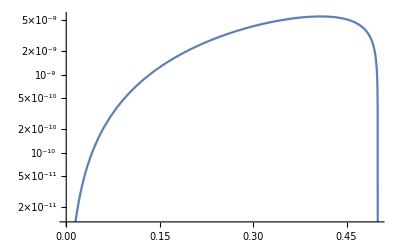

```mathematica
LogPlot[BRforpi0[1,x],{x,0,0.5}]
```

### Eta decays with meff

```mathematica
M = meff*22
```

22 meff

```mathematica
rate=M^2/(2 meta)*√Lambda[1,(m1/meta)^2,(m2/meta)^2]*1/(8 π)
```

(121 meff^2 √((-m1^2/meta^2-m2^2/meta^2+1)^2-(4 m1^2 m2^2)/meta^4))/(4 π meta)

```mathematica
rate/(1.31*10^-6)/.{meta-> 0.557,m1->0 ,m2-> 0}/.{meff-> meff*100*10^-9}
```

1.31962×10^-7 meff^2

### S2 decay with meff

```mathematica
M = meff
```

meff

```mathematica
rate=M^2/(2 m2)*1/(8 π)√Lambda[1,(m1/m2)^2,(mpi/m2)^2];
ratesimple=M^2/(2 m2)*1/(8 π)
```

meff^2/(16 π m2)

```mathematica
(3*10^10)/(ratesimple*1.52*10^24)/.{mpi-> 0.135,m1->0 ,m2-> 0.300}/.{meff-> meff*100*10^-9}
```

29.7625/meff^2

### Majorana Amplitudes

```mathematica
MAmp=((e ϵ Q Fpsi Mz)SpinorU[k2,m2].(Subscript[d, i,j] dm[μ].PL-Subscript[d, j,i] dm[μ].PR).SpinorV[k1,m1])/(Mzprime^2 -Pair[Momentum[k1+k2],Momentum[k1+k2]]);
MAmpC=ComplexConjugate[MAmp]/.{μ->μ2 ,Subscript[d, i,j]->Subscript[d, j,i],Subscript[d, j,i]->Subscript[d, i,j]};Msqr=FermionSpinSum[MAmpC MAmp]*PolarizationSum[μ,μ2,K]/.{DiracTrace-> Tr}/.{K-> k1+k2}//Contract;
DecayRateM=Msqr*SpinAverage*PS2*FluxFactor/.subP//Simplify
```

1/(8 π Mz (Mz^2-Mzprime^2)^2)e^2 Fpsi^2 Q^2 ϵ^2 √((m1^4-2 m1^2 (m2^2+Mz^2)+(m2^2-Mz^2)^2)/Mz^4) (-(m1^4+m1^2 (Mz^2-2 m2^2)+m2^4+m2^2 Mz^2-2 Mz^4) d_(j,i) d_(i,j)-3 m1 m2 Mz^2 d_(i,j)^2-3 m1 m2 Mz^2 d_(j,i)^2)

```mathematica
S[i_,j_]:=gx Subscript[U, s,j] Subscript[U, s,i]
```

```mathematica
SumM=DecayRateM/.{Subscript[d, i,j]-> S[5,5],Subscript[d, j,i]-> S[5,5]}/.{e-> √(alphaQED*4*π),gx->  √(alphaDark*4*π)}/.{Subscript[U, s,1]-> √(1-Subscript[U, s,2]^2-Subscript[U, s,3]^2-Subscript[U, s,4]^2-Subscript[U, s,5]^2)}/.{m1-> r1 Mz,m2-> r2 Mz}/.{r1-> -dR+r2}/.{r2-> (Rtot+dR)/2}//FullSimplify//Simplify//PowerExpand//FullSimplify
```

-(2 π alphaDark alphaQED √(dR^2-1) (dR^2+2) Fpsi^2 Mz^3 Q^2 (Rtot^2-1)^(3/2) ϵ^2 U_(s,5)^4)/((Mz^2-Mzprime^2)^2)

```mathematica
ratio=Sumee/SumM*3/.{dR-> 0,Rtot-> 0}//Simplify
```

0